# RandomGraph test

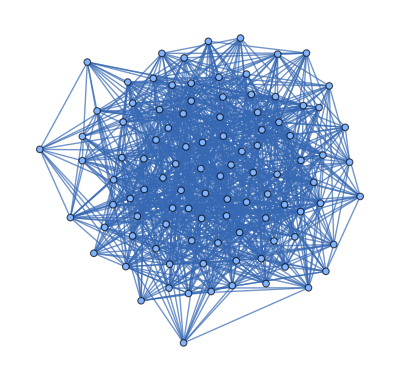

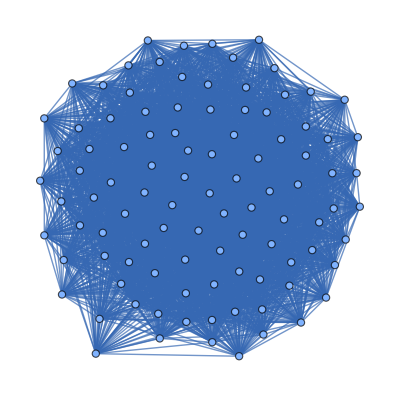

```mathematica
rg100a=RandomGraph[{100,1000}]
rg100b=RandomGraph[{100,3000}]
```

```mathematica
Timing[GraphDistance[rg100a,1,2]]
Timing[GraphDistance[rg100b,1,2]]
```

{0.000025,2}

{0.000022,1}

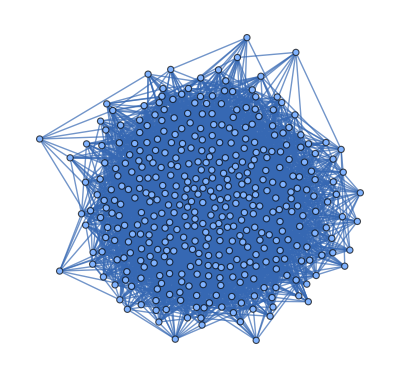

```mathematica
rg400a=RandomGraph[{400,4000}]
rg400b=RandomGraph[{400,12000}]
```

```mathematica
Timing[GraphDistance[rg400a,3,4]]
Timing[GraphDistance[rg400b,3,4]]
```

{0.000029,2}

{0.00016,2}

```mathematica
rg1000a=RandomGraph[{1000,10000}]
rg1000b=RandomGraph[{1000,30000}]
```

```mathematica
Timing[GraphDistance[rg1000a,6,8]]
Timing[GraphDistance[rg1000b,6,8]]
```

{0.000173,3}

{0.002537,2}